# Stage LMA 2A Centrale Marseille Mickaël LAVALLEE 10-07-17 Post traitement

## Test loi 403 OBJ : f=0.1⟶10, T=100 ⟶ 200, PEEK

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Boris\Documents\These\PyFFTDMA\Mickael\Python\FinalCampainResults\N8

```mathematica
ClearAll["Global`*"]
```

Création de la courbe à partir des fichier .csv

## Chargement 1

### Importation

```mathematica
Resultat5C1 =Import["ResultatFinal5C1.csv","Table"];
Resultat5C1=Transpose[Resultat5C1];
Resultat15C1=Import["ResultatFinal15C1.csv","Table"];
Resultat15C1=Transpose[Resultat15C1];
Resultat25C1 =Import["ResultatFinal25C1.csv","Table"];
Resultat25C1=Transpose[Resultat25C1];
```

```mathematica
ListFreq= Resultat5C1[[4]]+ⅈ*Resultat5C1[[4]];
```

```mathematica
données5C1=Resultat5C1[[2]]+ⅈ*Resultat5C1[[3]];
données15C1=Resultat15C1[[2]]+ⅈ*Resultat15C1[[3]];
données25C1=Resultat25C1[[2]]+ⅈ*Resultat25C1[[3]];
```

```mathematica
Data5C1 = Transpose@{ListFreq,données5C1};
Data15C1 = Transpose@{ListFreq,données15C1};
Data25C1 = Transpose@{ListFreq,données25C1};
```

### Courbe 5

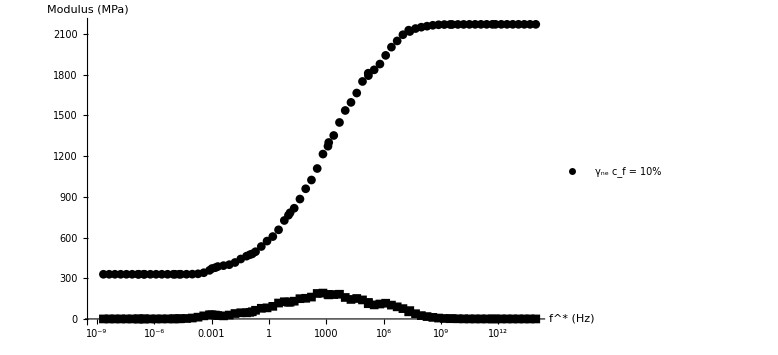

```mathematica
P5C1=ListLogLinearPlot[{Re[Data5C1],Im[Data5C1]},Joined->False,PlotRange->All,AxesLabel->{Style["f^* (Hz)",FontFamily->"Times New Roman",18],Style["Modulus (MPa)",FontFamily->"Times New Roman"],18},ImageSize->Large, Axes->True,PlotStyle->Black,AxesStyle->Directive[Black, 18,FontFamily->"Times New Roman"],PlotLegends->{Style["γ_ne c_f = 10%",FontFamily->"Times New Roman",18]},PlotMarkers->Automatic]
```

### Courbe 15

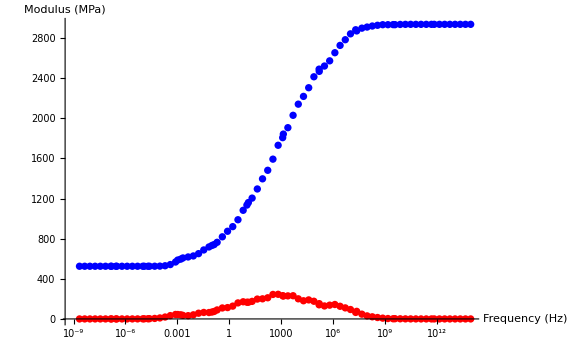

```mathematica
P15C1=ListLogLinearPlot[{Re[Data15C1],Im[Data15C1]},PlotStyle->{Blue,Red},Joined->False,PlotRange->All,AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

### Courbe 25

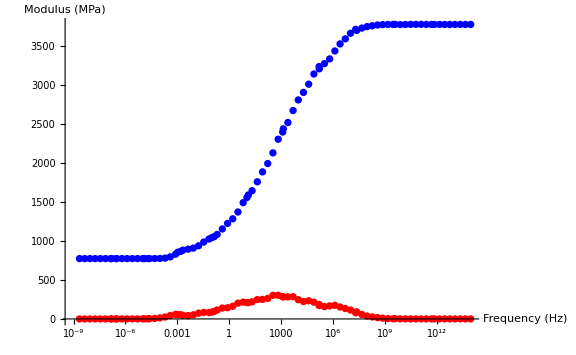

```mathematica
P25C1=ListLogLinearPlot[{Re[Data25C1],Im[Data25C1]},PlotStyle->{Blue,Red},Joined->False,PlotRange->All,AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

### Superposition des courbes

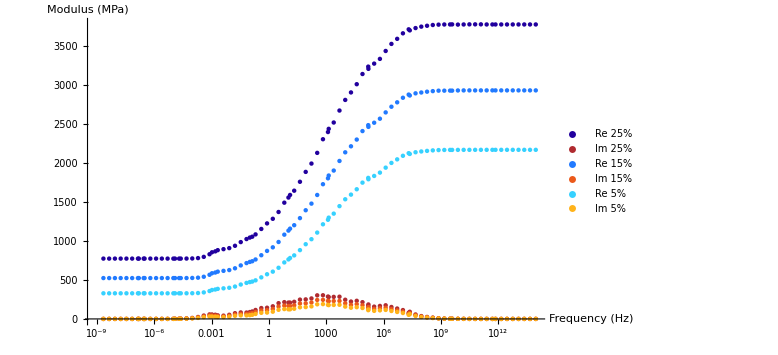

```mathematica
PlotExport=ListLogLinearPlot[{Re[Data25C1],Im[Data25C1],Re[Data15C1],Im[Data15C1],Re[Data5C1],Im[Data5C1]},PlotStyle->{RGBColor[0.13,0.,0.62],RGBColor[0.69,0.17,0.19],RGBColor[0.13,0.48,1],RGBColor[0.92,0.35,0.1],RGBColor[0.21,0.82,1.],RGBColor[1.,0.7,0.1]},Joined->False,PlotRange->All,PlotLegends->{"Re 25%","Im 25%","Re 15%","Im 15%","Re 5%","Im 5%"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

```mathematica
Export["ComparaisonC1.pdf",PlotExport]
```

ComparaisonC1.pdf

## Chargement 2

### Importation

```mathematica
Resultat5C2 =Import["ResultatFinal5C2.csv","Table"];
Resultat5C2=Transpose[Resultat5C2];
Resultat15C2=Import["ResultatFinal15C2.csv","Table"];
Resultat15C2=Transpose[Resultat15C2];
Resultat25C2 =Import["ResultatFinal25C2.csv","Table"];
Resultat25C2=Transpose[Resultat25C2];
```

```mathematica
ListFreq= Resultat5C2[[4]]+ⅈ*Resultat5C2[[4]];
```

```mathematica
données5C2=Resultat5C2[[2]]+ⅈ*Resultat5C2[[3]];
données15C2=Resultat15C2[[2]]+ⅈ*Resultat15C2[[3]];
données25C2=Resultat25C2[[2]]+ⅈ*Resultat25C2[[3]];
```

```mathematica
Data5C2 = Transpose@{ListFreq,données5C2};
Data15C2 = Transpose@{ListFreq,données15C2};
Data25C2 = Transpose@{ListFreq,données25C2};
```

### Courbe 5

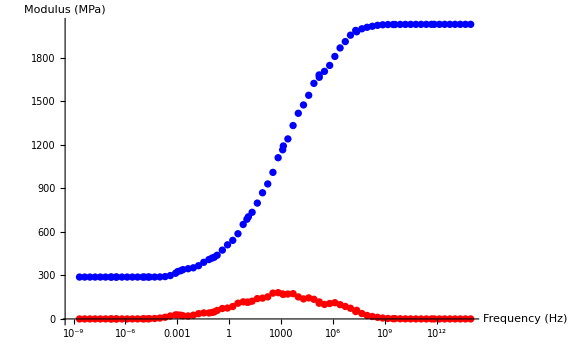

```mathematica
P5C2=ListLogLinearPlot[{Re[Data5C2],Im[Data5C2]},PlotStyle->{Blue,Red},Joined->False,PlotRange->All,AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

### Courbe 15

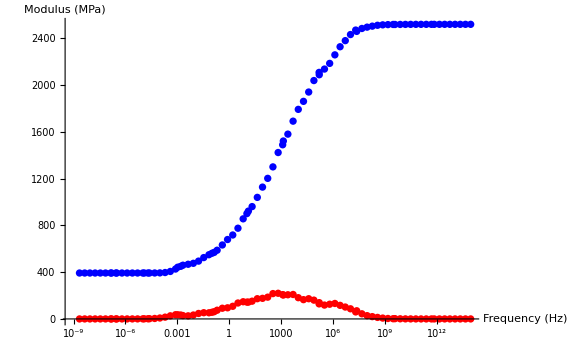

```mathematica
P15C2=ListLogLinearPlot[{Re[Data15C2],Im[Data15C2]},PlotStyle->{Blue,Red},Joined->False,PlotRange->All,AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

### Courbe 25

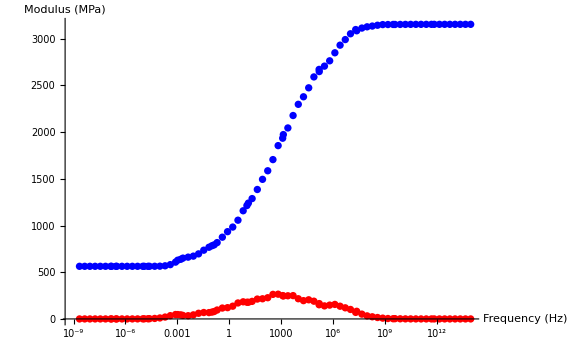

```mathematica
P25C2=ListLogLinearPlot[{Re[Data25C2],Im[Data25C2]},PlotStyle->{Blue,Red},Joined->False,PlotRange->All,AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

### Superposition des courbes

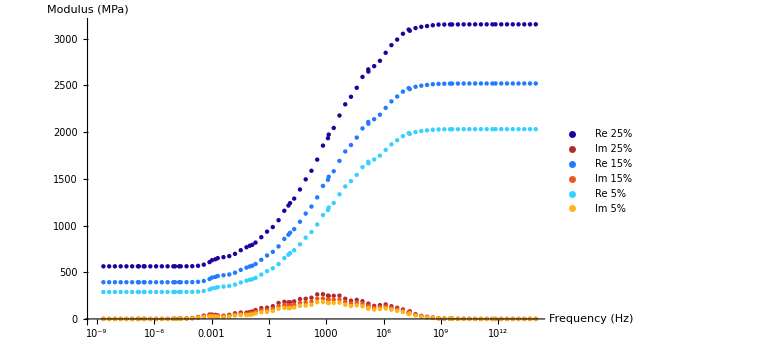

```mathematica
PlotExport=ListLogLinearPlot[{Re[Data25C2],Im[Data25C2],Re[Data15C2],Im[Data15C2],Re[Data5C2],Im[Data5C2]},PlotStyle->{RGBColor[0.13,0.,0.62],RGBColor[0.69,0.17,0.19],RGBColor[0.13,0.48,1],RGBColor[0.92,0.35,0.1],RGBColor[0.21,0.82,1.],RGBColor[1.,0.7,0.1]},Joined->False,PlotRange->All,PlotLegends->{"Re 25%","Im 25%","Re 15%","Im 15%","Re 5%","Im 5%"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

```mathematica
Export["ComparaisonC2.pdf",PlotExport]
```

ComparaisonC2.pdf

## Chargement 3

### Importation

```mathematica
Resultat5C3 =Import["ResultatFinal5C3.csv","Table"];
Resultat5C3=Transpose[Resultat5C3];
Resultat15C3=Import["ResultatFinal15C3.csv","Table"];
Resultat15C3=Transpose[Resultat15C3];
Resultat25C3 =Import["ResultatFinal25C3.csv","Table"];
Resultat25C3=Transpose[Resultat25C3];
```

```mathematica
ListFreq= Resultat5C3[[4]]+ⅈ*Resultat5C3[[4]];
```

```mathematica
données5C3=Resultat5C3[[2]]+ⅈ*Resultat5C3[[3]];
données15C3=Resultat15C3[[2]]+ⅈ*Resultat15C3[[3]];
données25C3=Resultat25C3[[2]]+ⅈ*Resultat25C3[[3]];
```

```mathematica
Data5C3 = Transpose@{ListFreq,données5C3};
Data15C3 = Transpose@{ListFreq,données15C3};
Data25C3 = Transpose@{ListFreq,données25C3};
```

### Courbe 5

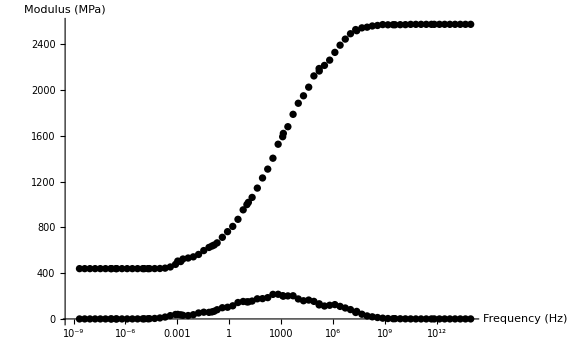

```mathematica
P5C3=ListLogLinearPlot[{Re[Data5C3],Im[Data5C3]},PlotStyle->{Black,Black},Joined->False,PlotRange->All,AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

### Courbe 15

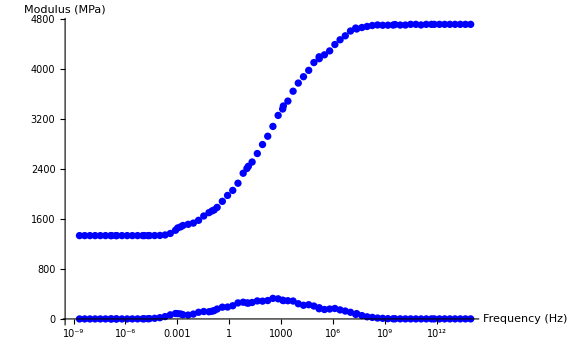

```mathematica
P15C3=ListLogLinearPlot[{Re[Data15C3],Im[Data15C3]},PlotStyle->{Blue},Joined->False,PlotRange->All,AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

### Courbe 25

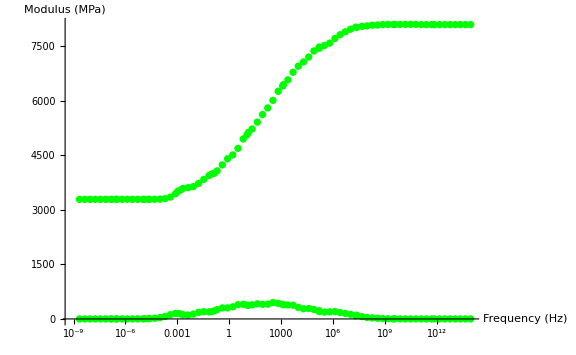

```mathematica
P25C3=ListLogLinearPlot[{Re[Data25C3],Im[Data25C3]},PlotStyle->{Green},Joined->False,PlotRange->All,AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

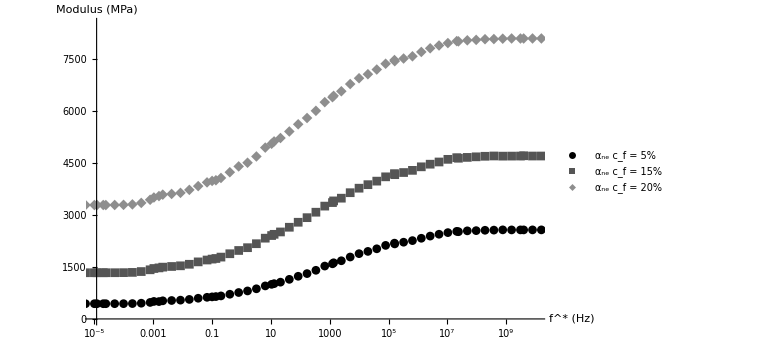

```mathematica
PC3Re =ListLogLinearPlot[{Re[Data5C3],Re[Data15C3],Re[Data25C3]},Joined->False,PlotRange->{{0.00001,10000000000},{0,8500}},AxesLabel->{Style["f^* (Hz)",FontFamily->"Times New Roman",18],Style["Modulus (MPa)",FontFamily->"Times New Roman"],18},ImageSize->Large, Axes->True,PlotStyle->{Black,Lighter[Black],Lighter[Lighter[Black]]},AxesStyle->Directive[Black, 18,FontFamily->"Times New Roman"],PlotLegends->{Style["α_ne c_f = 5%",FontFamily->"Times New Roman",18],Style["α_ne c_f = 15%",FontFamily->"Times New Roman",18],Style["α_ne c_f = 20%",FontFamily->"Times New Roman",18]},PlotMarkers->Automatic]
```

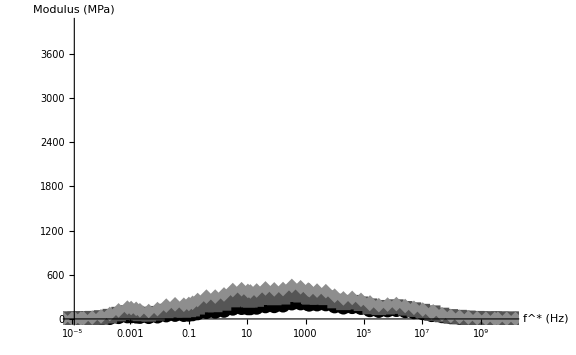

```mathematica
PC3Im =ListLogLinearPlot[{Im[Data5C3],Im[Data15C3],Im[Data25C3]},Joined->False,PlotRange->{{0.00001,10000000000},{0,4000}},PlotStyle->{Black,Lighter[Black],Lighter[Lighter[Black]]},AxesLabel->{Style["f^* (Hz)",FontFamily->"Times New Roman",18],Style["Modulus (MPa)",FontFamily->"Times New Roman"],18},ImageSize->Large, Axes->True,PlotStyle->Black,AxesStyle->Directive[Black, 18,FontFamily->"Times New Roman"],PlotMarkers->{Automatic,15}]
```

### Superposition des courbes

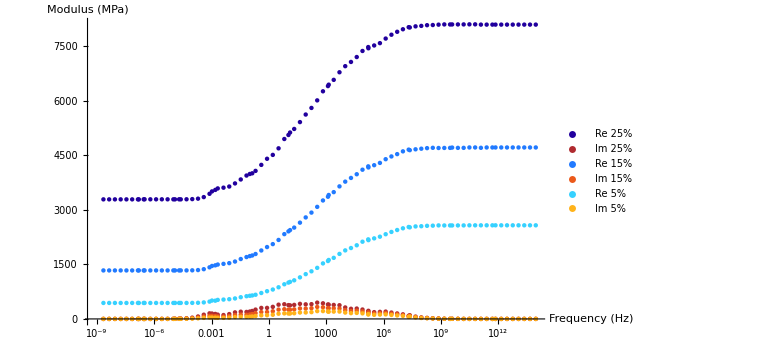

```mathematica
PlotExport=ListLogLinearPlot[{Re[Data25C3],Im[Data25C3],Re[Data15C3],Im[Data15C3],Re[Data5C3],Im[Data5C3]},PlotStyle->{RGBColor[0.13,0.,0.62],RGBColor[0.69,0.17,0.19],RGBColor[0.13,0.48,1],RGBColor[0.92,0.35,0.1],RGBColor[0.21,0.82,1.],RGBColor[1.,0.7,0.1]},Joined->False,PlotRange->All,PlotLegends->{"Re 25%","Im 25%","Re 15%","Im 15%","Re 5%","Im 5%"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

```mathematica
Export["ComparaisonC3.pdf",PlotExport]
```

ComparaisonC3.pdf

## Chargement 4 - 1

### Importation

```mathematica
Resultat5C4 =Import["ResultatFinal5C4.csv","Table"];
Resultat5C4=Transpose[Resultat5C4];
Resultat15C4=Import["ResultatFinal15C4.csv","Table"];
Resultat15C4=Transpose[Resultat15C4];
Resultat25C4 =Import["ResultatFinal25C4.csv","Table"];
Resultat25C4=Transpose[Resultat25C4];
```

```mathematica
ListFreq= Resultat5C4[[4]]+ⅈ*Resultat5C4[[4]];
```

```mathematica
données5C4=Resultat5C4[[2]]+ⅈ*Resultat5C4[[3]];
données15C4=Resultat15C4[[2]]+ⅈ*Resultat15C4[[3]];
données25C4=Resultat25C4[[2]]+ⅈ*Resultat25C4[[3]];
```

```mathematica
Data5C4 = Transpose@{ListFreq,données5C4};
Data15C4 = Transpose@{ListFreq,données15C4};
Data25C4 = Transpose@{ListFreq,données25C4};
```

### Courbe 5

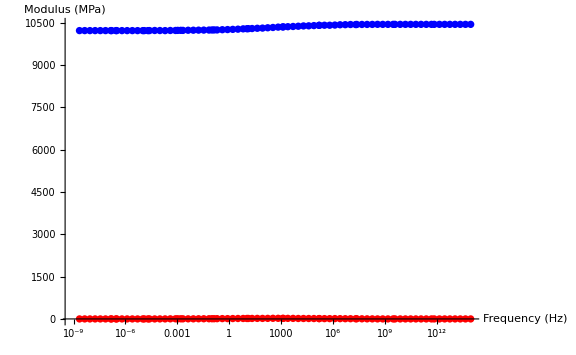

```mathematica
P5C4=ListLogLinearPlot[{Re[Data5C4],Im[Data5C4]},PlotStyle->{Blue,Red},Joined->False,PlotRange->All,AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

### Courbe 15

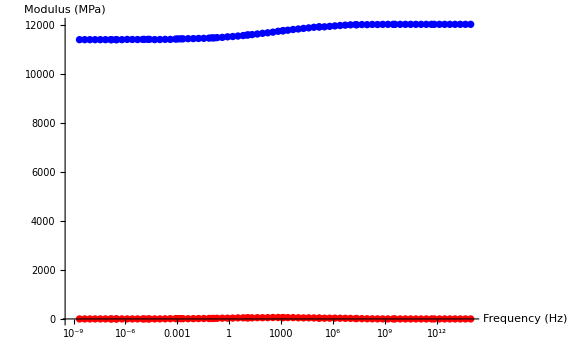

```mathematica
P15C4=ListLogLinearPlot[{Re[Data15C4],Im[Data15C4]},PlotStyle->{Blue,Red},Joined->False,PlotRange->All,AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

### Courbe 25

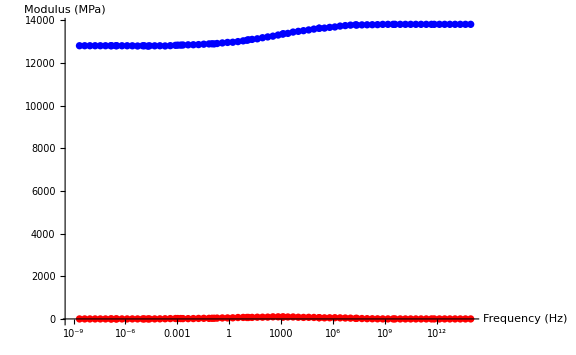

```mathematica
P25C4=ListLogLinearPlot[{Re[Data25C4],Im[Data25C4]},PlotStyle->{Blue,Red},Joined->False,PlotRange->All,AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

### Superposition des courbes

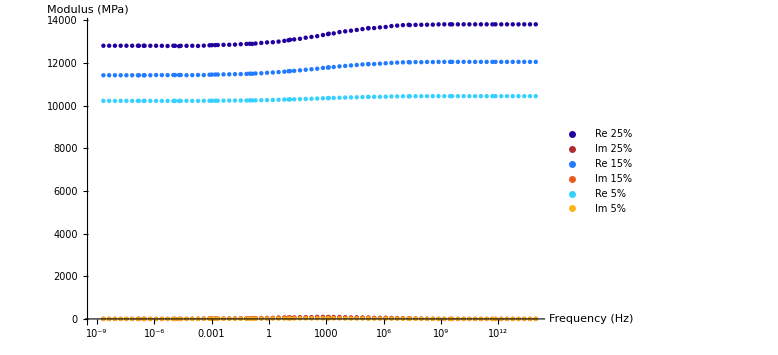

```mathematica
PlotExport=ListLogLinearPlot[{Re[Data25C4],Im[Data25C4],Re[Data15C4],Im[Data15C4],Re[Data5C4],Im[Data5C4]},PlotStyle->{RGBColor[0.13,0.,0.62],RGBColor[0.69,0.17,0.19],RGBColor[0.13,0.48,1],RGBColor[0.92,0.35,0.1],RGBColor[0.21,0.82,1.],RGBColor[1.,0.7,0.1]},Joined->False,PlotRange->All,PlotLegends->{"Re 25%","Im 25%","Re 15%","Im 15%","Re 5%","Im 5%"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

```mathematica
Export["ComparaisonC4.pdf",PlotExport]
```

ComparaisonC4.pdf

## Chargement 4 - 2

### Importation

```mathematica
Resultat5C5 =Import["ResultatFinal5C5.csv","Table"];
Resultat5C5=Transpose[Resultat5C5];
Resultat15C5=Import["ResultatFinal15C5.csv","Table"];
Resultat15C5=Transpose[Resultat15C5];
Resultat25C5 =Import["ResultatFinal25C5.csv","Table"];
Resultat25C5=Transpose[Resultat25C5];
```

```mathematica
ListFreq= Resultat5C5[[4]]+ⅈ*Resultat5C5[[4]];
```

```mathematica
données5C5=Resultat5C5[[2]]+ⅈ*Resultat5C5[[3]];
données15C5=Resultat15C5[[2]]+ⅈ*Resultat15C5[[3]];
données25C5=Resultat25C5[[2]]+ⅈ*Resultat25C5[[3]];
```

```mathematica
Data5C5 = Transpose@{ListFreq,données5C5};
Data15C5 = Transpose@{ListFreq,données15C5};
Data25C5 = Transpose@{ListFreq,données25C5};
```

### Courbe 5

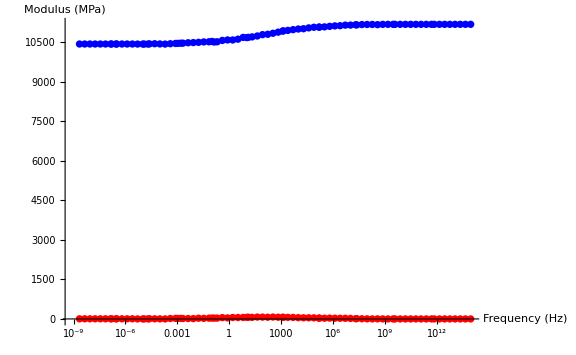

```mathematica
P5C5=ListLogLinearPlot[{Re[Data5C5],Im[Data5C5]},PlotStyle->{Blue,Red},Joined->False,PlotRange->All,AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

### Courbe 15

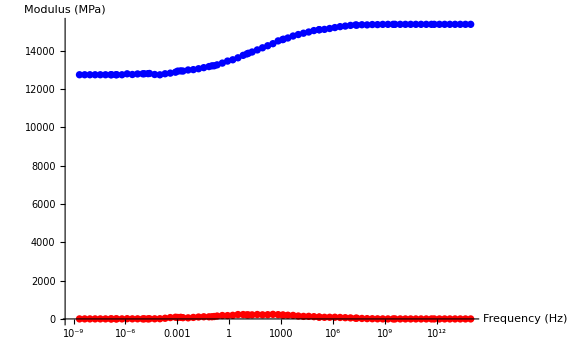

```mathematica
P15C5=ListLogLinearPlot[{Re[Data15C5],Im[Data15C5]},PlotStyle->{Blue,Red},Joined->False,PlotRange->All,AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

### Courbe 25

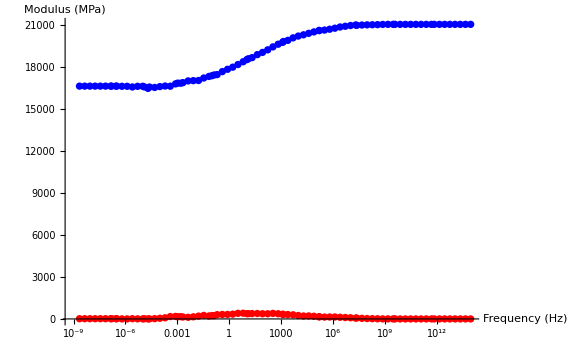

```mathematica
P25C5=ListLogLinearPlot[{Re[Data25C5],Im[Data25C5]},PlotStyle->{Blue,Red},Joined->False,PlotRange->All,AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

### Superposition des courbes

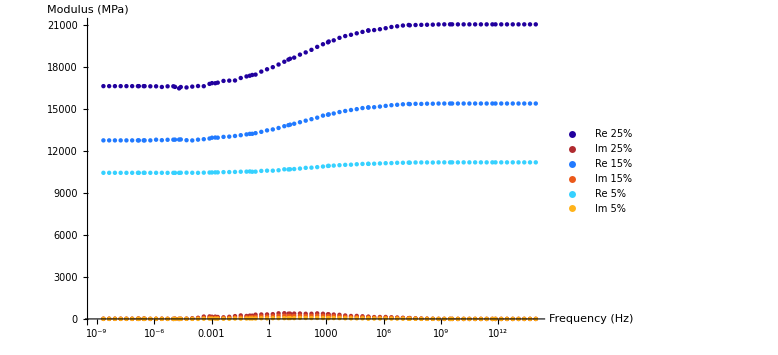

```mathematica
PlotExport=ListLogLinearPlot[{Re[Data25C5],Im[Data25C5],Re[Data15C5],Im[Data15C5],Re[Data5C5],Im[Data5C5]},PlotStyle->{RGBColor[0.13,0.,0.62],RGBColor[0.69,0.17,0.19],RGBColor[0.13,0.48,1],RGBColor[0.92,0.35,0.1],RGBColor[0.21,0.82,1.],RGBColor[1.,0.7,0.1]},Joined->False,PlotRange->All,PlotLegends->{"Re 25%","Im 25%","Re 15%","Im 15%","Re 5%","Im 5%"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"},ImageSize->Large, Axes->True]
```

```mathematica
Export["ComparaisonC5.pdf",PlotExport]
```

ComparaisonC5.pdf

```mathematica
Branche1[μ_,τ_,ω_] :=(ⅈ *ω*μ)/(τ+ⅈ *ω);
```

```mathematica
F[x_,a_,b_]:=1/(a Sqrt[2 π])Exp[(-(x-b)^2)/(2 a^2)]
```

```mathematica
val1 =6.1
val2 = 0
```

6.1

0

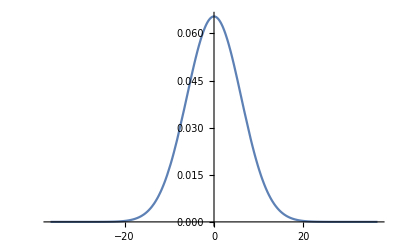

```mathematica
Plot[F[x,val1,val2],{x,-6*val1,6*val1},PlotRange->All]
```

```mathematica
NbTemps = 150;
Valeurs = (6*val1)/NbTemps;
ListAbsysses = {};
ListFacteurs = {};
For [i=0,i≤2*NbTemps,i++,ListAbsysses  = Append[ListAbsysses,-6*val1+i*Valeurs]]
For [i=1,i≤2*NbTemps+1,i++,ListFacteurs = Append[ListFacteurs,F[ListAbsysses [[i]],val1,val2]]]
```

```mathematica
ListAbsysses = N[Exp[ListAbsysses]];
ListFacteurs=ListFacteurs/Total[N[ListFacteurs]];
```

```mathematica
StringSpectr="SpectralModel[k0_,μ_,τ_,ω_]:=k0+"
```

SpectralModel[k0_,μ_,τ_,ω_]:=k0+

```mathematica
For[i=1,i≤2*NbTemps,i++,StringSpectr=StringSpectr<>"Branche1[μ*ListFacteurs[["<>ToString[i]<>"]],τ*ListAbsysses[["<>ToString[i]<>"]],ω]+"]
```

```mathematica
StringSpectr=StringSpectr<>"Branche1[μ*Last[ListFacteurs],τ*Last[ListAbsysses],ω]";
```

```mathematica
DefineSpectr[]:=ToExpression[StringSpectr]
```

```mathematica
DefineSpectr[]
```

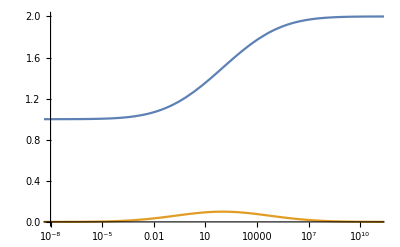

```mathematica
LogLinearPlot[{Re[SpectralModel[1,1,100,ω]],Im[SpectralModel[1,1,100,ω]]},{ω,0.0000000001,10000000000000},PlotRange->{{0.00000001,100000000000},{0,2}}]
```

```mathematica
Ke = ({{1/6, -1/3, 1/6, 0, 0, 0}, {-1/3, 2/3, -1/3, 0, 0, 0}, {1/6, -1/3, 1/6, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}});
Kt=({{1/2, 0, -1/2, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {-1/2, 0, 1/2, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0}});
Kl=({{0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1}});
```

```mathematica
Tensor[α_,β_,γ_,δ_,δp_]:=({{β/2+δ/2, γ/(√2), β/2-δ/2, 0, 0, 0}, {γ/(√2), α, γ/(√2), 0, 0, 0}, {β/2-δ/2, γ/(√2), β/2+δ/2, 0, 0, 0}, {0, 0, 0, δp, 0, 0}, {0, 0, 0, 0, δ, 0}, {0, 0, 0, 0, 0, δp}});
```

```mathematica
L0 [α0_,β0_,λ0_,δ0_,γ0_]:= Tensor[α0,β0,λ0,δ0,γ0]
```

```mathematica
Lv0[α0_,β0_,λ0_,δ0_,γ0_] := FullSimplify[L0[α0,β0,λ0,δ0,γ0]];
```

```mathematica
TensorExpressionKt[δL_,δη_,ω_] := SpectralModel[0,δL,δη,ω]Kt
```

```mathematica
TensorExpressionKt[δL,δη,ω]//MatrixForm;
```

```mathematica
TensorExpressionKl[γL_,γη_,ω_] := SpectralModel[0,γL,γη,ω]Kl
```

```mathematica
TensorExpressionKl[δL,δη,ω]//MatrixForm;
```

```mathematica
TensorExpressionKe[αL_,αη_,ω_] := SpectralModel[0,αL,αη,ω]Ke
```

```mathematica
Lve[α0_,β0_,λ0_,δ0_,γ0_,αL_,αη_,δL_,δη_,γL_,γη_,ω_]:=Lv0[α0,β0,λ0,δ0,γ0]+TensorExpressionKe[αL,αη,ω]+TensorExpressionKl[γL,γη,ω]+TensorExpressionKt[δL,δη,ω]
```

```mathematica
V1 =({{0}, {0}, {0}, {1}, {0}, {1}}); V2 =({{0}, {0}, {0}, {0}, {1}, {0}});V3 =({{-0.5}, {1}, {-0.5}, {0}, {0}, {0}});V5 =({{1}, {1}, {1}, {0}, {0}, {0}});
V51 = ({{1}, {0}, {1}, {0}, {0}, {0}});V52 = ({{0}, {1}, {0}, {0}, {0}, {0}});
```

```mathematica
1/((V51.{1}).V51.{1})(Tensor[α,β,γ,δ,δp].V5.{1}).V51.{1}
```

1/2 (2 β+√2 γ)

```mathematica
1/((V52.{1}).V52.{1})(Tensor[α,β,γ,δ,δp].V5.{1}).V52.{1}
```

α+√2 γ

```mathematica
1/((V3.{1}).V3.{1})(Tensor[α,β,γ,δ,δp].V3.{1}).V3.{1}//FullSimplify
```

0.+0.666667 α+0.333333 β-0.942809 γ

```mathematica
Identification du modèle
```

```mathematica
5%
```

```mathematica
A=Solve[0.6666666666666666 α0+0.3333333333333333 β0-0.9428090415820632 λ0==Last[Re[Data5C3]][[2]]&&α0+√2 λ0==Mean[Re[Data5C5]][[2]]&&1/2 (2 β0+√2 λ0)==Mean[Re[Data5C4]][[2]]];
α05 = (α0/.A).{1};
β05 = (β0/.A).{1};
λ05  =(λ0/.A).{1};
δ05=Last[Re[Data5C2]][[2]];
γ05 = Last[Re[Data5C1]][[2]];
αL5 = First[Re[Data5C3]][[2]]-Last[Re[Data5C3]][[2]];
δL5 = First[Re[Data5C2]][[2]]-δ05;
γL5 = First[Re[Data5C1]][[2]]-δ05;
```

```mathematica
v1load5[P_,γη5_]:=1/((V1.{1}).V1.{1})(Lve[α05,β05,λ05,δ05,γ05,αL5,αη5,δL5,δη5,γL5,γη5,P].V1.{1}).V1.{1};
v2load5[P_,δη5_]:=1/((V2.{1}).V2.{1})(Lve[α05,β05,λ05,δ05,γ05,αL5,αη5,δL5,δη5,γL5,γη5,P].V2.{1}).V2.{1};
v3load5[P_,αη5_]:=1/((V3.{1}).V3.{1})(Lve[α05,β05,λ05,δ05,γ05,αL5,αη5,δL5,δη5,γL5,γη5,P].V3.{1}).V3.{1};
Lve[1,1,1,1,1,1,1,1,1,1,1,1]
```

{{1.33333+0.0663831 ⅈ,0.54044-0.0331916 ⅈ,-0.166667-0.0331916 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.54044-0.0331916 ⅈ,1.33333+0.0663831 ⅈ,0.54044-0.0331916 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.166667-0.0331916 ⅈ,0.54044-0.0331916 ⅈ,1.33333+0.0663831 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.5+0.0995747 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.5+0.0995747 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.5+0.0995747 ⅈ}}

```mathematica
A=NonlinearModelFit[Re[Data5C1],Re[v1load5[ω,γη5]],γη5,ω];
γη5=γη5/.(A[[1]][[2]]);
B=NonlinearModelFit[Re[Data5C2],Re[v2load5[ω,δη5]],δη5,ω];
δη5=δη5/.(B[[1]][[2]]);
CC=NonlinearModelFit[Re[Data5C3],Re[v3load5[ω,αη5]],αη5,ω];
αη5=αη5/.(CC[[1]][[2]]);
```

```mathematica
v1load5[P_]=1/((V1.{1}).V1.{1})(Lve[α05,β05,λ05,δ05,γ05,αL5,αη5,δL5,δη5,γL5,γη5,P].V1.{1}).V1.{1};
v2load5[P_]=1/((V2.{1}).V2.{1})(Lve[α05,β05,λ05,δ05,γ05,αL5,αη5,δL5,δη5,γL5,γη5,P].V2.{1}).V2.{1};
v3load5[P_]=1/((V3.{1}).V3.{1})(Lve[α05,β05,λ05,δ05,γ05,αL5,αη5,δL5,δη5,γL5,γη5,P].V3.{1}).V3.{1};
v51load5[P_]=1/((V51.{1}).V51.{1})(Lve[α05,β05,λ05,δ05,γ05,αL5,αη5,δL5,δη5,γL5,γη5,P].V5.{1}).V51.{1};
v52load5[P_]=1/((V52.{1}).V52.{1})(Lve[α05,β05,λ05,δ05,γ05,αL5,αη5,δL5,δη5,γL5,γη5,P].V5.{1}).V52.{1};
```

```mathematica
Chargement1 -> {0,0,0,1,1,0}
```

```mathematica
M5C1=LogLinearPlot[{Re[v1load5[ω]],Im[v1load5[ω]]},{ω,0.0000001,10000000000000},PlotLegends->{"µ' Model","µ'' Model"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"}];
```

```mathematica
Chargement2 -> {0,0,0,0,1,0}
```

```mathematica
M5C2=LogLinearPlot[{Re[v2load5[ω]],Im[v2load5[ω]]},{ω,0.0000001,10000000000000},PlotLegends->{"µ' Model","µ'' Model"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"}];
```

```mathematica
Chargement3 -> {-0.5,-0.5,1,0,0,0}
```

```mathematica
M5C3=LogLinearPlot[{Re[v3load5[ω]],Im[v3load5[ω]]},{ω,0.0000001,10000000000000},AxesLabel->{Style["f^* (Hz)",FontFamily->"Times New Roman",18],Style["Modulus (MPa)",FontFamily->"Times New Roman"],18},ImageSize->Large, Axes->True,PlotStyle->Black,AxesStyle->Directive[Black, 18,FontFamily->"Times New Roman"],PlotLegends->{Style["α_ve c_f = 5%",FontFamily->"Times New Roman",18]}];
```

```mathematica
Chargement5.1 -> {1,1,0,0,0,0} 
Projection après application du chargement5
```

```mathematica
M5C4=LogLinearPlot[{Re[v51load5[ω]],Im[v51load5[ω]]},{ω,0.0000001,10000000000000},PlotLegends->{"µ' Model","µ'' Model"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"}];
```

```mathematica
Chargement5.1 -> {0,0,1,0,0,0} 
Projection après application du chargement5
```

```mathematica
M5C5=LogLinearPlot[{Re[v52load5[ω]],Im[v52load5[ω]]},{ω,0.0000001,10000000000000},PlotLegends->{"µ' Model","µ'' Model"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"}];
```

```mathematica
15%
```

```mathematica
A=Solve[0.6666666666666666 α0+0.3333333333333333 β0-0.9428090415820632 λ0==Last[Re[Data15C3]][[2]]&&α0+√2 λ0==Mean[Re[Data15C5]][[2]]&&1/2 (2 β0+√2 λ0)==Mean[Re[Data15C4]][[2]]];
α015 = (α0/.A).{1};
β015 = (β0/.A).{1};
λ015  =(λ0/.A).{1};
δ015=Last[Re[Data15C2]][[2]];
γ015 = Last[Re[Data15C1]][[2]];
αL15 = First[Re[Data15C3]][[2]]-Last[Re[Data15C3]][[2]];
δL15 = First[Re[Data15C2]][[2]]-δ015;
γL15 = First[Re[Data15C1]][[2]]-γ015;
```

```mathematica
αL15+α015
αL15
First[Data15C3]
Last[Data15C3]
```

9506.78

3378.89

{7.19686×10^11+7.19686×10^11 ⅈ,4711.44+0.699984 ⅈ}

{2.80308×10^-7+2.80308×10^-7 ⅈ,1332.56+0.0415897 ⅈ}

```mathematica
v1load15[P_,γη15_]:=1/((V1.{1}).V1.{1})(Lve[α015,β015,λ015,δ015,γ015,αL15,αη15,δL15,δη15,γL15,γη15,P].V1.{1}).V1.{1};
v2load15[P_,δη15_]:=1/((V2.{1}).V2.{1})(Lve[α015,β015,λ015,δ015,γ015,αL15,αη15,δL15,δη15,γL15,γη15,P].V2.{1}).V2.{1};
v3load15[P_,αη15_]:=1/((V3.{1}).V3.{1})(Lve[α015,β015,λ015,δ015,γ015,αL15,αη15,δL15,δη15,γL15,γη15,P].V3.{1}).V3.{1};
```

```mathematica
A=NonlinearModelFit[Re[Data15C1],Re[v1load15[ω,γη15]],γη15,ω];
γη15=γη15/.(A[[1]][[2]]);
B=NonlinearModelFit[Re[Data15C2],Re[v2load15[ω,δη15]],δη15,ω];
δη15=δη15/.(B[[1]][[2]]);
CC=NonlinearModelFit[Re[Data15C3],Re[v3load15[ω,αη15]],αη15,ω];
αη15=αη15/.(CC[[1]][[2]]);
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
v1load15[P_]=1/((V1.{1}).V1.{1})(Lve[α015,β015,λ015,δ015,γ015,αL15,αη15,δL15,δη15,γL15,γη15,P].V1.{1}).V1.{1};
v2load15[P_]=1/((V2.{1}).V2.{1})(Lve[α015,β015,λ015,δ015,γ015,αL15,αη15,δL15,δη15,γL15,γη15,P].V2.{1}).V2.{1};
v3load15[P_]=1/((V3.{1}).V3.{1})(Lve[α015,β015,λ015,δ015,γ015,αL15,αη15,δL15,δη15,γL15,γη15,P].V3.{1}).V3.{1};
v51load15[P_]=1/((V51.{1}).V51.{1})(Lve[α015,β015,λ015,δ015,γ015,αL15,αη15,δL15,δη15,γL15,γη15,P].V5.{1}).V51.{1};
v52load15[P_]=1/((V52.{1}).V52.{1})(Lve[α015,β015,λ015,δ015,γ015,αL15,αη15,δL15,δη15,γL15,γη15,P].V5.{1}).V52.{1};
```

```mathematica
Chargement1 -> {0,0,0,1,1,0}
```

```mathematica
M15C1=LogLinearPlot[{Re[v1load15[ω]],Im[v1load15[ω]]},{ω,0.0000001,10000000000000},PlotLegends->{"µ' Model","µ'' Model"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"}];
```

```mathematica
Chargement2 -> {0,0,0,0,1,0}
```

```mathematica
M15C2=LogLinearPlot[{Re[v2load15[ω]],Im[v2load15[ω]]},{ω,0.0000001,10000000000000},PlotLegends->{"µ' Model","µ'' Model"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"}];
```

```mathematica
Chargement3 -> {-0.5,-0.5,1,0,0,0}
```

```mathematica
M15C3=LogLinearPlot[{Re[v3load15[ω]],Im[v3load15[ω]]},{ω,0.0000001,10000000000000},AxesLabel->{Style["f^* (Hz)",FontFamily->"Times New Roman",18],Style["Modulus (MPa)",FontFamily->"Times New Roman"],18},ImageSize->Large, Axes->True,PlotStyle->Lighter[Black],AxesStyle->Directive[Black, 18,FontFamily->"Times New Roman"],PlotLegends->{Style["α_ve c_f = 15%",FontFamily->"Times New Roman",18]}];
```

```mathematica
Chargement5.1 -> {1,1,0,0,0,0} 
Projection après application du chargement5
```

```mathematica
M15C4=LogLinearPlot[{Re[v51load15[ω]],Im[v51load15[ω]]},{ω,0.0000001,10000000000000},PlotLegends->{"µ' Model","µ'' Model"},PlotStyle->Blue,AxesLabel->{"Frequency (Hz)","Modulus (MPa)"}];
```

```mathematica
Chargement5.1 -> {0,0,1,0,0,0} 
Projection après application du chargement5
```

```mathematica
M15C5=LogLinearPlot[{Re[v52load15[ω]],Im[v52load15[ω]]},{ω,0.0000001,10000000000000},PlotLegends->{"µ' Model","µ'' Model"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"}];
```

```mathematica
25%
```

```mathematica
A=Solve[0.6666666666666666 α0+0.3333333333333333 β0-0.9428090415820632 λ0==Last[Re[Data25C3]][[2]]&&α0+√2 λ0==Mean[Re[Data25C5]][[2]]&&1/2 (2 β0+√2 λ0)==Mean[Re[Data25C4]][[2]]];
α025 = (α0/.A).{1};
β025 = (β0/.A).{1};
λ025  =(λ0/.A).{1};
δ025=Last[Re[Data25C2]][[2]];
γ025 = Last[Re[Data25C1]][[2]];
αL25 = First[Re[Data25C3]][[2]]-Last[Re[Data25C3]][[2]];
δL25 = First[Re[Data25C2]][[2]]-δ025;
γL25 = First[Re[Data25C1]][[2]]-γ025;
```

```mathematica
0.6666666666666666 α025+0.3333333333333333 β025-0.9428090415820632 λ025
```

3287.01

```mathematica
Last[Re[Data25C3]][[2]]
```

3287.01

```mathematica
γL25+γ025
γL25
First[Data25C1]
Last[Data25C1]
```

3782.53

3007.51

{7.19686×10^11+7.19686×10^11 ⅈ,3782.53+0.222646 ⅈ}

{2.80308×10^-7+2.80308×10^-7 ⅈ,775.015+0.0299571 ⅈ}

```mathematica
v1load25[P_,γη25_]:=1/((V1.{1}).V1.{1})(Lve[α025,β025,λ025,δ025,γ025,αL25,αη25,δL25,δη25,γL25,γη25,P].V1.{1}).V1.{1};
v2load25[P_,δη25_]:=1/((V2.{1}).V2.{1})(Lve[α025,β025,λ025,δ025,γ025,αL25,αη25,δL25,δη25,γL25,γη25,P].V2.{1}).V2.{1};
v3load25[P_,αη25_]:=1/((V3.{1}).V3.{1})(Lve[α025,β025,λ025,δ025,γ025,αL25,αη25,δL25,δη25,γL25,γη25,P].V3.{1}).V3.{1};
```

```mathematica
A=NonlinearModelFit[Re[Data25C1],Re[v1load25[ω,γη25]],γη25,ω];
γη25=γη25/.(A[[1]][[2]]);
B=NonlinearModelFit[Re[Data25C2],Re[v2load25[ω,δη25]],δη25,ω];
δη25=δη25/.(B[[1]][[2]]);
CC=NonlinearModelFit[Re[Data25C3],Re[v3load25[ω,αη25]],αη25,ω];
αη25=αη25/.(CC[[1]][[2]]);
```

```mathematica
v1load25[P_]=1/((V1.{1}).V1.{1})(Lve[α025,β025,λ025,δ025,γ025,αL25,αη25,δL25,δη25,γL25,γη25,P].V1.{1}).V1.{1};
v2load25[P_]=1/((V2.{1}).V2.{1})(Lve[α025,β025,λ025,δ025,γ025,αL25,αη25,δL25,δη25,γL25,γη25,P].V2.{1}).V2.{1};
v3load25[P_]=1/((V3.{1}).V3.{1})(Lve[α025,β025,λ025,δ025,γ025,αL25,αη25,δL25,δη25,γL25,γη25,P].V3.{1}).V3.{1};
v51load25[P_]=1/((V51.{1}).V51.{1})(Lve[α025,β025,λ025,δ025,γ025,αL25,αη25,δL25,δη25,γL25,γη25,P].V5.{1}).V51.{1};
v52load25[P_]=1/((V52.{1}).V52.{1})(Lve[α025,β025,λ025,δ025,γ025,αL25,αη25,δL25,δη25,γL25,γη25,P].V5.{1}).V52.{1};
```

```mathematica
Chargement1 -> {0,0,0,1,1,0}
```

```mathematica
M25C1=LogLinearPlot[{Re[v1load25[ω]],Im[v1load25[ω]]},{ω,0.0000001,10000000000000},PlotLegends->{"µ' Model","µ'' Model"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"}];
```

```mathematica
Chargement2 -> {0,0,0,0,1,0}
```

```mathematica
M25C2=LogLinearPlot[{Re[v2load25[ω]],Im[v2load25[ω]]},{ω,0.0000001,10000000000000},PlotLegends->{"µ' Model","µ'' Model"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"}];
```

```mathematica
Chargement3 -> {-0.5,-0.5,1,0,0,0}
```

```mathematica
M25C3=LogLinearPlot[{Re[v3load25[ω]],Im[v3load25[ω]]},{ω,0.0000001,10000000000000},AxesLabel->{Style["f^* (Hz)",FontFamily->"Times New Roman",18],Style["Modulus (MPa)",FontFamily->"Times New Roman"],18},ImageSize->Large, Axes->True,PlotStyle->Lighter[Lighter[Black]],AxesStyle->Directive[Black, 18,FontFamily->"Times New Roman"],PlotLegends->{Style["α_ve c_f = 25%",FontFamily->"Times New Roman",18]}];
M25C3Im = LogLinearPlot[{Im[v3load25[ω]],Im[v3load25[ω]]},{ω,0.0000001,10000000000000},PlotLegends->{"µ' Model","µ'' Model"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"}];
```

```mathematica
Chargement5.1 -> {1,1,0,0,0,0} 
Projection après application du chargement5
```

```mathematica
M25C4=LogLinearPlot[{Re[v51load25[ω]],Im[v51load25[ω]]},{ω,0.0000001,10000000000000},PlotLegends->{"µ' Model","µ'' Model"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"}];
```

```mathematica
Chargement5.1 -> {0,0,1,0,0,0} 
Projection après application du chargement5
```

```mathematica
M25C5=LogLinearPlot[{Re[v52load25[ω]],Im[v52load25[ω]]},{ω,0.0000001,10000000000000},PlotLegends->{"µ' Model","µ'' Model"},AxesLabel->{"Frequency (Hz)","Modulus (MPa)"}];
```

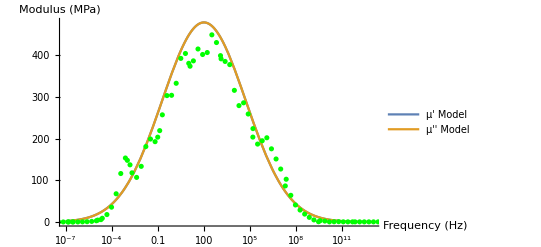

```mathematica
Show[M25C3Im,P25C3]
```

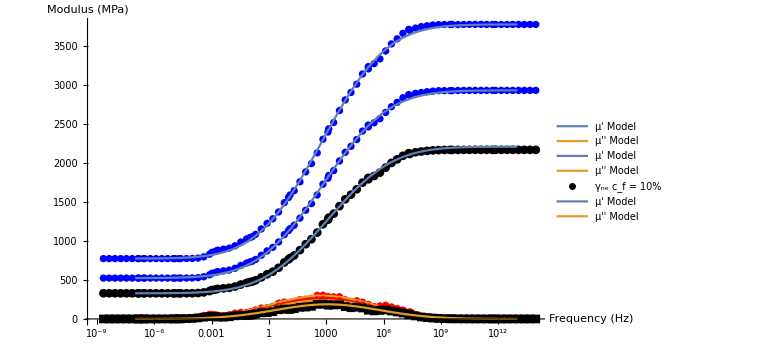

```mathematica
Show[P25C1,M25C1,P15C1,M15C1,P5C1,M5C1]
```

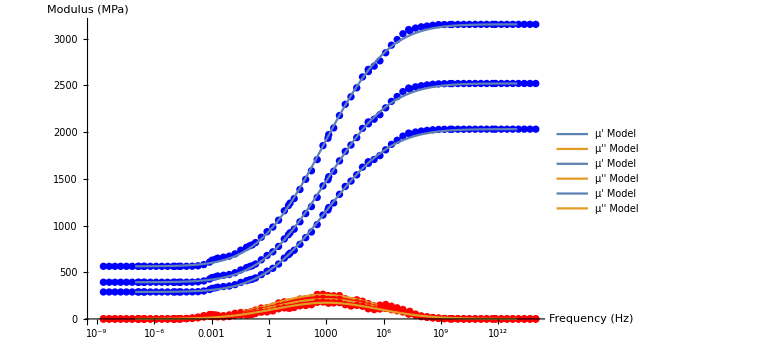

```mathematica
Show[P25C2,M25C2,P15C2,M15C2,P5C2,M5C2]
```

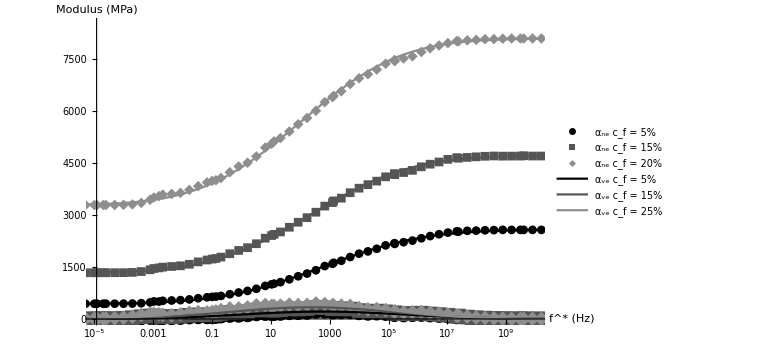

```mathematica
PlotExport=Show[PC3Re,PC3Im,M5C3,M15C3,M25C3,ImageSize-> Large]
```

```mathematica
Export["Fitted3DSpectral.eps",PlotExport]
```

Fitted3DSpectral.eps

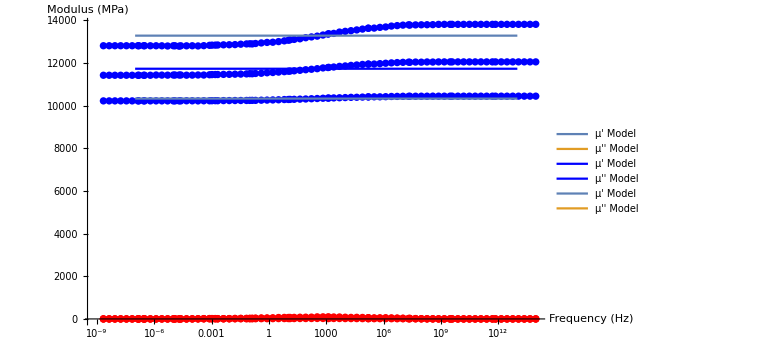

```mathematica
Show[P25C4,M25C4,P15C4,M15C4,P5C4,M5C4]
```

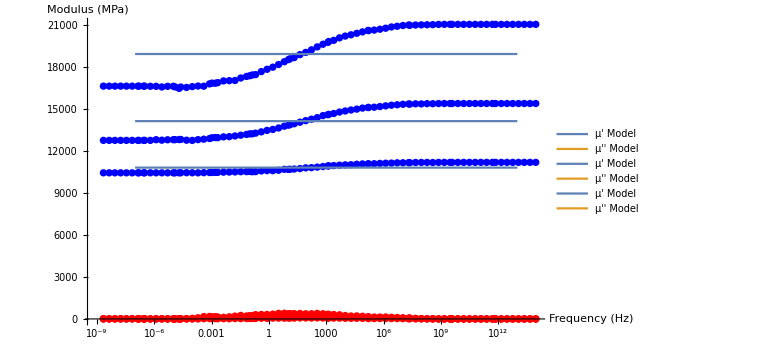

```mathematica
Show[P25C5,M25C5,P15C5,M15C5,P5C5,M5C5]
```

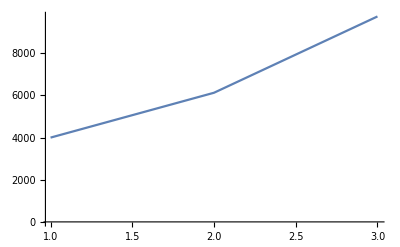

```mathematica
α0List = {α05,α015,α025};
ListPlot[α0List,Joined->True,PlotRange->All]
```

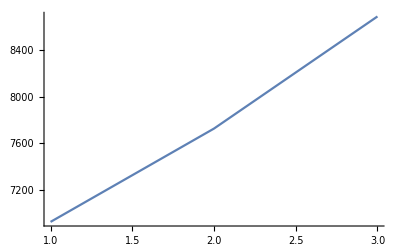

```mathematica
β0List = {β05,β015,β025};
ListPlot[β0List,Joined->True,PlotRange->All]
```

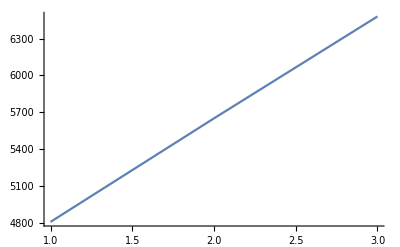

```mathematica
λ0List = {λ05,λ015,λ025};
ListPlot[λ0List,Joined->True,PlotRange->All]
```

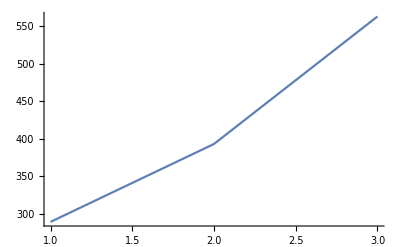

```mathematica
δ0List = {δ05,δ015,δ025};
ListPlot[δ0List,Joined->True,PlotRange->All]
```

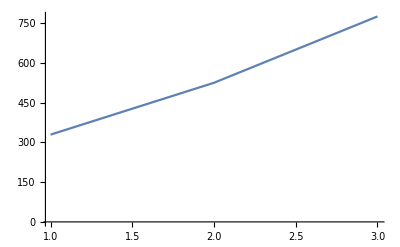

```mathematica
γ0List = {γ05,γ015,γ025};
ListPlot[γ0List,Joined->True,PlotRange->All]
```

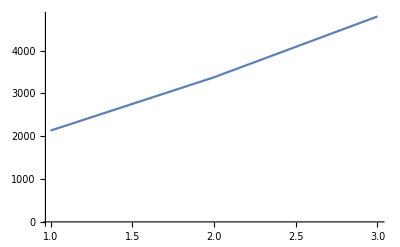

```mathematica
αLList = {αL5,αL15,αL25};
ListPlot[αLList,Joined->True,PlotRange->All]
```

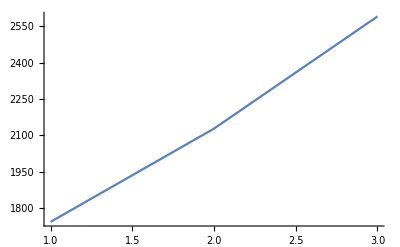

```mathematica
δLList = {δL5,δL15,δL25};
ListPlot[δLList,Joined->True,PlotRange->All]
```

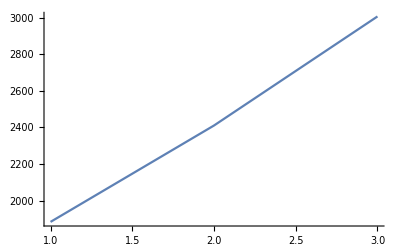

```mathematica
γLList = {γL5,γL15,γL25};
ListPlot[γLList,Joined->True,PlotRange->All]
```

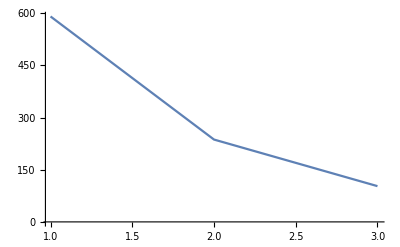

```mathematica
αηList = {αη5,αη15,αη25};
ListPlot[αηList,Joined->True,PlotRange->All]
```

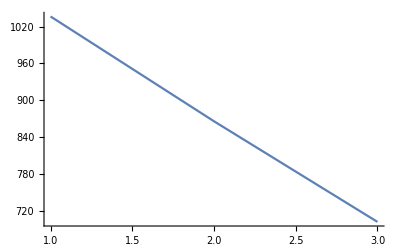

```mathematica
δηList = {δη5,δη15,δη25};
ListPlot[δηList,Joined->True,PlotRange->All]
```

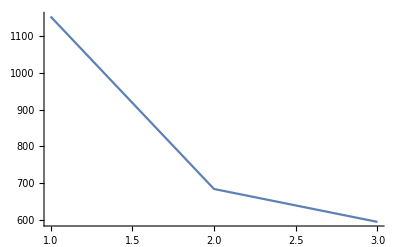

```mathematica
γηList = {γη5,γη15,γη25};
ListPlot[γηList,Joined->True,PlotRange->All]
```

```mathematica
α0List = {α05,α015,α025};
β0List = {β05,β015,β025};
λ0List = {λ05,λ015,λ025};
δ0List = {δ05,δ015,δ025};
γ0List = {γ05,γ015,γ025};
αLList = {αL5,αL15,αL25};
δLList = {δL5,δL15,δL25};
γLList = {γL5,γL15,γL25};
αηList = {αη5,αη15,αη25};
δηList = {δη5,δη15,δη25};
γηList = {γη5,γη15,γη25};
```

```mathematica
ParametersMatrix={{5,15,25},α0List,β0List,λ0List,δ0List,γ0List,αLList,δLList,γLList,αηList,δηList,γηList,{val1,val1,val1}};
```

```mathematica
ParametersMatrix//MatrixForm
```

(5 | 15 | 25
3999.46 | 6127.89 | 9748.06
6922.76 | 7726.24 | 8691.4
4809.82 | 5651.32 | 6479.39
288.822 | 392.941 | 563.318
329.241 | 524.847 | 775.015
2133.25 | 3378.89 | 4799.98
1743. | 2127.93 | 2590.71
1883.27 | 2410.78 | 3007.51
590.53 | 236.685 | 102.77
1036.71 | 865.733 | 701.583
1152.45 | 684.794 | 595.541
6.1 | 6.1 | 6.1)

```mathematica
Export["ParametersMatrix8.xml",ParametersMatrix]
```

ParametersMatrix8.xml

```mathematica
s
```

s